```mathematica
fulldata= Import["C:\\Users\\Jesus Enrique\\Documents\\Wolfram Desktop\\Population1.csv"];
FiltRegInd[ind_]:=GatherBy[Select[fulldata,#[[6]]==ind&],First];
coloresregion = {{"EAP",CMYKColor[0,.85,1,0,0.6]},{"ECA",CMYKColor[0,.54,.95,0,0.6]},{"LAC",CMYKColor[1,.11,.38,.01,0.6]},{"MENA",CMYKColor[.91,0,.97,0,0.6]},{"SAR",CMYKColor[.56,.99,0,0,0.6]},{"SSA",CMYKColor[1,.44,.52,.22,0.6]}}
```

{{EAP,CMYKColor[0, 0.85, 1, 0, 0.6]},{ECA,CMYKColor[0, 0.54, 0.95, 0, 0.6]},{LAC,CMYKColor[1, 0.11, 0.38, 0.01, 0.6]},{MENA,CMYKColor[0.91, 0, 0.97, 0, 0.6]},{SAR,CMYKColor[0.56, 0.99, 0, 0, 0.6]},{SSA,CMYKColor[1, 0.44, 0.52, 0.22, 0.6]}}

```mathematica
framestopdf[filename_,plotlist_]:=Table[Export[filename<>ToString[i]<>".pdf",plotlist[[i]]],{i,1,plotlist//Length}]
```

```mathematica
urbgrowth = FiltRegInd["SP.URB.GROW"];
popgrowth = FiltRegInd["SP.POP.GROW"];
pop = FiltRegInd["SP.POP.TOTL"];
```

```mathematica
plotgrowth[region_,year_]:=Module[{plotpoints,paises},
paises = urbgrowth[[region,;;,4]];
plotpoints = Transpose[{popgrowth[[region,;;,year]],urbgrowth[[region,;;,year]]}];
ListPlot[Table[Callout[plotpoints[[i]],paises[[i]],Automatic,LabelStyle->{8}],{i,1,plotpoints//Length}],PlotStyle->coloresregion[[region,2]], PlotRange->{{-10,10},{-10,10}},PlotLabel->ToString[year+1953]<>" "<>urbgrowth[[region,1,1]],
AxesLabel->{"% PG","%UG"},LabelStyle->RGBColor[.55,.55,.55],ImageSize->Large]
]

plotgrowthnolabel[region_,year_]:=Module[{plotpoints,paises},
paises = urbgrowth[[region,;;,4]];
plotpoints = Transpose[{popgrowth[[region,;;,year]],urbgrowth[[region,;;,year]]}];
ListPlot[Table[plotpoints[[i]],{i,1,plotpoints//Length}],PlotStyle->coloresregion[[region,2]], PlotRange->{{-10,10},{-10,10}},PlotLabel->ToString[year+1953]<>" "<>urbgrowth[[region,1,1]],
AxesLabel->{"% PG","%UG"},LabelStyle->RGBColor[.55,.55,.55],ImageSize->Large]
]


plotgrowthbubc[region_,year_]:=Module[{plotpoints,paises},
paises = urbgrowth[[region,;;,4]];

plotpoints = Table[{popgrowth[[region,i,year]],urbgrowth[[region,i,year]],pop[[region,i,year]]},{i,1,popgrowth[[region]]//Length}];

BubbleChart[Table[Callout[plotpoints[[i]],paises[[i]],LabelStyle->{4}],{i,1,plotpoints//Length}],{PlotRange->{{-2,8},{-2,8}},PlotLabel->ToString[year+1953],
AxesLabel->{"% PG","%UG"},ImageSize->Large,ChartStyle->coloresregion[[region,2]]}]

]
```

```mathematica
plotsallregions = Table[plotgrowthbubc[reg,year],{year,58,58},{reg,1,6}];
fullcolorsplots = Table[Show@@plotsallregions[[i]],{i,1,plotsallregions//Length}];
ListAnimate[fullcolorsplots]
```

Part::partd: Part specification GatherBy[Select[$Failed,#1⟦6⟧==SP.URB.GROW&],First]⟦1,1;;All,4⟧ is longer than depth of object.

Part::partd: Part specification GatherBy[Select[$Failed,#1⟦6⟧==SP.POP.GROW&],First]⟦1,1,58⟧ is longer than depth of object.

Part::partd: Part specification GatherBy[Select[$Failed,#1⟦6⟧==SP.URB.GROW&],First]⟦1,1,58⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 58 of #1⟦6⟧==SP.POP.GROW& does not exist.

Part::partw: Part 58 of #1⟦6⟧==SP.URB.GROW& does not exist.

Part::partw: Part 58 of #1⟦6⟧==SP.POP.TOTL& does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
framestopdf["bubblepop",fullcolorsplots]
```

{bubblepop1.pdf}

```mathematica
plotsallregions = Table[plotgrowth[reg,year],{year,7,63,5},{reg,3,3}];
fullcolorsplots = Table[Show@@plotsallregions[[i]],{i,1,plotsallregions//Length}];
ListAnimate[fullcolorsplots]
```

```mathematica
framestopdf["popgrowLAC",fullcolorsplots]
```

{popgrowLAC1.pdf,popgrowLAC2.pdf,popgrowLAC3.pdf,popgrowLAC4.pdf,popgrowLAC5.pdf,popgrowLAC6.pdf,popgrowLAC7.pdf,popgrowLAC8.pdf,popgrowLAC9.pdf,popgrowLAC10.pdf,popgrowLAC11.pdf,popgrowLAC12.pdf}

```mathematica
Export["popgrowallregions.avi",ListAnimate[fullcolorsplots],FrameRate->0.2]
```

popgrowallregions.avi

```mathematica
plotsallregions = Table[plotgrowthnolabel[reg,year],{year,7,63,1},{reg,1,6}];
fullcolorsplots = Table[Show@@plotsallregions[[i]],{i,1,plotsallregions//Length}];
ListAnimate[fullcolorsplots]
```

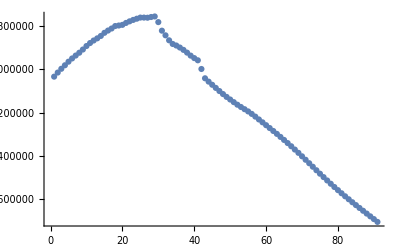

```mathematica
ListPlot[pop[[2,6,7;;]]]
```

```mathematica
pop[[1,4]]
```

{East Asia & Pacific,China,China,CHN,Population, total,SP.POP.TOTL,667070000,660330000,665770000,682335000,698355000,715185000,735400000,754550000,774510000,796025000,818315000,841105000,862030000,881940000,900350000,916395000,930685000,943455000,956165000,969005000,981235000,993885000,1008630000,1023310000,1036825000,1051040000,1066790000,1084035000,1101630000,1118650000,1135185000,1150780000,1164970000,1178440000,1191835000,1204855000,1217550000,1230075000,1241935000,1252735000,1262645000,1271850000,1280400000,1288400000,1296075000,1303720000,1311020000,1317885000,1324655000,1331260000,1337705000,1344130000,1350695000,1357380000,1364270000,1371220000,1378665000,1383981000,1388738000,1392929000,1396550000,1399628000,1402197000,1404286000,1405936000,1407176000,1408028000,1408505000,1408628000,1408417000,1407888000,1407052000,1405905000,1404437000,1402658000,1400593000,1398288000,1395758000,1393004000,1390039000,1386862000,1383460000,1379794000,1375818000,1371514000,1366864000,1361856000,1356498000,1350804000,1344791000,1338155000}